#### Start of notebook

```mathematica
ClearAll["Global`*"];
hybridORhomogenous = "hybrid";
GetPhotonNumber[treeVec_List]:=∑_(i=1)^Length[treeVec] ∏_(j=1)^i treeVec[[j]];
costFunc[skr_List,Latt_List,kappa_Integer,tauph_List,Ltot_List,mI_List,mII_List]:=Module[{out,dim},
(*This `costFunc` is used for cases when cost function is not calculated within the C++ calculation, e.g., purely maximising the SKR.*)
dim=Dimensions[skr];
out=ConstantArray[0,dim];
Quiet[
Do[
out[[i,All]]=(Latt[[i]](mI[[i,All]]+kappa*mII[[i,All]]))/(skr[[i,All]]Ltot[[i,All]]tauph[[i]]);
,{i,1,dim[[1]]}];
,General::infy];
out
];

doExport=True;(*Change this accordingly*)
Needs["GeneralUtilities`"];(*Reference: https://mathematica.stackexchange.com/questions/206173/increasing-the-length-of-frame-ticks*)

(*1. Open the file browser to select the.dat file*)(*The second argument provides a starting directory and a file type filter*)filename=SystemDialogInput["FileOpen",{NotebookDirectory[],{"Data Files (*.dat)"->{"*.dat"},"All Files (*.*)"->{"*"}}}];

(*2. Check if the user canceled the selection*)
If[filename===$Canceled,Print["File selection canceled."];
Abort[];];

(*3. Open the selected file in binary format*)
file=OpenRead[filename,BinaryFormat->True];

(*4. Generate the hash and print info*)
fileHash=FileHash[filename,"CRC32","HexString"];

Print["Selected file: ",filename];
Print["File Hash (CRC32): ",fileHash];
Print["Current working directory: ",Directory[]];

fm2[name_String,size_:8,opacity_:0,thickness_:1.1]:=ResourceFunction["PolygonMarker"][name,Offset@size,{Dynamic@EdgeForm[{CurrentValue["Color"],JoinForm["Round"],AbsoluteThickness[thickness],Opacity[1]}],Dynamic@FaceForm@Lighter[Opacity[opacity,CurrentValue["Color"]],0.75]}];
(*Reference: https://resources.wolframcloud.com/FunctionRepository/resources/PolygonMarker*)
(*Reference: https://mathematica.stackexchange.com/questions/270160/how-to-make-transparent-markers-without-plotted-lines-going-through-them*)
```

Selected file: D:\QEC_Codes\Thesis\7-1-3 (CORRECTED)\secret_key_rate\build\Release\binary_data\latest_Nmax_300_d1.dat

File Hash (CRC32): 1b5bc54c

Current working directory: C:\Users\SBihan

#### Read the data from the file and then close it

```mathematica
Clear[fileCounter,tmp];
fileCounter=0;
reencodingError={};
reencodingErrorFactor={};
teleportedErrorFactor={};
Latt={};
etad={};
tauph={};
tauss={};
size={};
treeSize={};
SKR={};
cost={};
L0={};
ntot={};
Ltot={};
treeVecs={};
c={};
pTransSum={};
logicalError={};
etae={};
f={};
fileExists=FileExistsQ[filename];

precisionType="Real64";

While[fileExists,
tmp = BinaryRead[file, precisionType];
If[SameQ[tmp,EndOfFile],Print["End of file reached."];Break[];];
AppendTo[reencodingError,tmp];
AppendTo[reencodingErrorFactor,BinaryRead[file,"Integer32"]];
AppendTo[teleportedErrorFactor,BinaryRead[file,"Integer32"]];
AppendTo[Latt,BinaryRead[file,precisionType]];
AppendTo[etad,BinaryRead[file,precisionType]];
AppendTo[tauph,BinaryRead[file,precisionType]];
AppendTo[tauss,BinaryRead[file,precisionType]];
AppendTo[size,BinaryRead[file,"UnsignedInteger64"]];
AppendTo[treeSize,BinaryRead[file,"UnsignedInteger64"]];
AppendTo[SKR,BinaryReadList[file,precisionType,size[[fileCounter+1]]]];
AppendTo[cost,BinaryReadList[file,precisionType,size[[fileCounter+1]]]];
AppendTo[L0,BinaryReadList[file,precisionType,size[[fileCounter+1]]]];
AppendTo[ntot,BinaryReadList[file,"Integer32",size[[fileCounter+1]]]];
AppendTo[Ltot,BinaryReadList[file,precisionType,size[[fileCounter+1]]]];
AppendTo[treeVecs,ConstantArray[0,{size[[fileCounter+1]],treeSize[[fileCounter+1]]}]];
Do[
treeVecs[[fileCounter+1]][[i,All]]=BinaryReadList[file,"UnsignedInteger16",treeSize[[fileCounter+1]]]
,{i,1,size[[fileCounter+1]]}];
AppendTo[c,BinaryReadList[file,"Integer32",size[[fileCounter+1]]]];
AppendTo[pTransSum,BinaryReadList[file,precisionType,size[[fileCounter+1]]]];
AppendTo[logicalError,BinaryReadList[file,precisionType,size[[fileCounter+1]]]];
AppendTo[etae,BinaryReadList[file,precisionType,size[[fileCounter+1]]]];
AppendTo[f,BinaryReadList[file,precisionType,size[[fileCounter+1]]]];

fileCounter++;
]
Print["The while loop was executed ",fileCounter," times."];
Clear[tmp];
Close[file];
```

End of file reached.

The while loop was executed 5 times.

#### Sort the data according to ascending order of reencodingError

```mathematica
reencodingErrorFactor=reencodingErrorFactor[[Ordering@reencodingError]];
teleportedErrorFactor=teleportedErrorFactor[[Ordering@reencodingError]];
Latt=Latt[[Ordering@reencodingError]];
etad=etad[[Ordering@reencodingError]];
tauph=tauph[[Ordering@reencodingError]];
tauss=tauss[[Ordering@reencodingError]];
size=size[[Ordering@reencodingError]];
treeSize=treeSize[[Ordering@reencodingError]];
SKR=SKR[[Ordering@reencodingError]];
cost=cost[[Ordering@reencodingError]];
L0=L0[[Ordering@reencodingError]];
ntot=ntot[[Ordering@reencodingError]];
Ltot=Ltot[[Ordering@reencodingError]];
treeVecs=treeVecs[[Ordering@reencodingError]];
c=c[[Ordering@reencodingError]];
pTransSum=pTransSum[[Ordering@reencodingError]];
logicalError=logicalError[[Ordering@reencodingError]];
etae=etae[[Ordering@reencodingError]];
f=f[[Ordering@reencodingError]];
reencodingError=reencodingError[[Ordering@reencodingError]];
Print["Data has been sorted."];
```

Data has been sorted.

#### Prepare plotting parameter values

```mathematica
Clear[plotmarkers,RED,PUR,BLU,BLA,GRE, plotstyle,imagesize,framestyle,labelstyle,plotlegends];
RED=RGBColor["#EE351E"];
PUR=RGBColor["#995CB3"];
BLU=RGBColor["#234AA3"];
BLA=RGBColor["#211E1E"];
GRE = RGBColor["#3ac9b0"];
imagesize=400;
background = White;
tickfontsize = 20;
axistitlefontsize = 20;
legendfontsize =16;
plotmarkers=Module[{g,prim},g=fm2[#];
prim=First[g];(*preserve original colors& shapes*)Graphics[prim,PlotRange->{{-1.25,1.25},{-1.25,1.25}},(*padded bounding box*)ImagePadding->2,(*prevents edge clipping*)AspectRatio->1,ImageSize->14                                (*adjust if needed*)]]&/@{"FourPointedStar","Circle","Diamond","Square","Triangle"};
linethickness=AbsoluteThickness[1.1];
plotstyle={{linethickness,BLA},{linethickness,BLU},{linethickness,RED},{linethickness,PUR}, {linethickness,GRE}};
labelstyle={FontSize->legendfontsize,FontFamily->"Times",GrayLevel[0],FrameMargins->{{0,0},{0,0}}};
framestyle=Directive[GrayLevel[0],AbsoluteThickness[1.1]];
plotlegends=PointLegend[{"ϵ_r=0.01%","ϵ_r=0.03%","ϵ_r=0.05%","ϵ_r=0.1%", "ϵ_r=0.2%"},LegendMarkerSize->{12,12},LegendLayout->{"Column",Spacings->0.3},(*tighter spacing*)
LegendFunction->(Framed[#,(*framing box*)RoundingRadius->10,(*rounded*)FrameStyle->Black,Background->White,(*opaque*)FrameMargins->0]&)];
```

#### Plot SKR

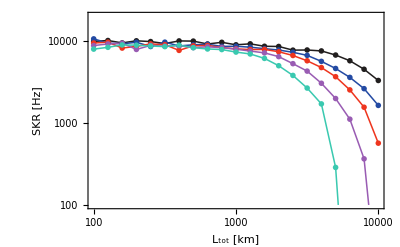

```mathematica
Clear[labeledTicks,unlabeledTicks,myTicks];
(*https://mathematica.stackexchange.com/questions/241982/use-custom-ticks-on-frameticks-on-loglogplot-but-preserving-the-log-tick-marks*)
plottitle=Style["Secret Key Rate Characteristics",Bold,Black,22,FontFamily->"Times"];
labeledTicks=Table[{10^i,Superscript[10,i]},{i,-20,15}];
unlabeledTicks=Flatten[Table[{k*j,Null},{k,2,9},{j,labeledTicks[[All,1]]}],1];
myTicks=Join[labeledTicks,unlabeledTicks];
plot…SKR=ListLogLogPlot[Table[Transpose[{Ltot[[i]]/1*^3,SKR[[i]]}],{i,1,fileCounter}], Background->background,PlotRange->{{Ltot[[1,1]]/1*^3,Ltot[[1,-1]]/1*^3},{1*^2,2*^4}},GridLines->{All,All},Frame->True,FrameLabel->{Style["L_tot [km]",Bold,Black, axistitlefontsize,FontFamily->"Times"],Style["SKR [Hz]",Bold,Black, axistitlefontsize, FontFamily->"Times"]},ImageSize->imagesize,FrameTicksStyle->{{Directive[Black,FontSize->tickfontsize],Automatic},{Directive[Black,FontSize->tickfontsize],Automatic}},FrameTicks->{{myTicks,None},{myTicks,None}},Joined->True,PlotMarkers->plotmarkers,LabelStyle->labelstyle,PlotStyle->plotstyle,FrameStyle->framestyle,PlotLegends->Placed[plotlegends,{0.2,0.42}],PlotRangePadding->{{0.1,0.1},{0.25,0.1}}]
```

```mathematica
Export["E:\\Documents\\OneDrive - bracu.ac.bd\\Documents\\Quantum Computing\\Paper-Springer\\Corrected\\Plots (SVG)\\SKR_7-1-3.svg",plot…SKR,"SVG"]
```

E:\Documents\OneDrive - bracu.ac.bd\Documents\Quantum Computing\Paper-Springer\Corrected\Plots (SVG)\SKR_7-1-3.svg

#### Plot Cost

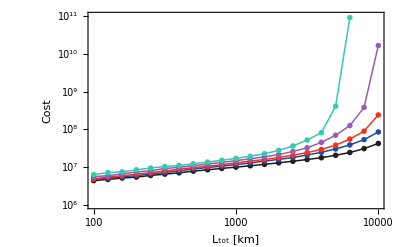

```mathematica
plottitle=Style["Cost Variation",Bold,Black,22,FontFamily->"Times"];
plot…cost=ListLogLogPlot[Table[Transpose[{Ltot[[i]]/1*^3,cost[[i]]}],{i,1,fileCounter}], Background->background,PlotRange->{{Ltot[[1,1]]/1*^3,Ltot[[1,-1]]/1*^3},{1*^6,1*^11}},GridLines->{All,All},PlotMarkers->plotmarkers,Joined->True,Frame->True,FrameLabel->{Style["L_tot [km]",Bold,Black,axistitlefontsize,FontFamily->"Times"],Style["Cost",Bold,Black,axistitlefontsize,FontFamily->"Times"]},ImageSize->imagesize,FrameTicksStyle->{{Directive[Black,FontSize->tickfontsize],Automatic},{Directive[Black,FontSize->tickfontsize],Automatic}},FrameTicks->{{myTicks,None},{myTicks,None}},PlotStyle->plotstyle,LabelStyle->labelstyle,FrameStyle->framestyle,PlotLegends->Placed[plotlegends,{0.18,0.63}],PlotRangePadding->{{0.1,0.1},{0.25,0.1}}]
(*Export["C:\\Users\\jen_7\\Documents\\GitHub\\one-way-quantum-repeaters\\plot_cost.pdf",plot…cost];*)
```

```mathematica
Export["E:\\Documents\\OneDrive - bracu.ac.bd\\Documents\\Quantum Computing\\Paper-Springer\\Corrected\\Plots (SVG)\\Cost_7-1-3.svg",plot…cost,"SVG"]
```

E:\Documents\OneDrive - bracu.ac.bd\Documents\Quantum Computing\Paper-Springer\Corrected\Plots (SVG)\Cost_7-1-3.svg

#### Plot L_0

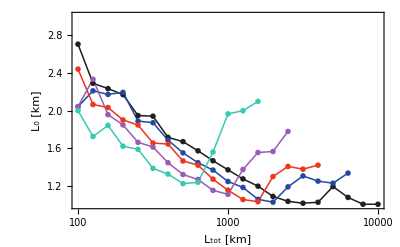

```mathematica
plot…L0=ListLogLinearPlot[Table[Transpose[{Ltot[[i]]/1*^3,L0[[i]]/1*^3}],{i,1,fileCounter}], Background->background,PlotRange->{{Ltot[[1,1]]/1*^3,Ltot[[1,-1]]/1*^3},{1,3}},GridLines->{All,All},PlotMarkers->plotmarkers,Joined->True,Frame->True,FrameLabel->{"L_tot [km]","L_0 [km]"},ImageSize->imagesize,FrameTicks->{Automatic,{myTicks,None}},PlotStyle->plotstyle,LabelStyle->labelstyle,PlotLegends->Placed[plotlegends,{0.85,0.65}],PlotRangePadding->{{0.1,0.1},{0.25,0.1}}]
(*Export["C:\\Users\\jen_7\\Documents\\GitHub\\one-way-quantum-repeaters\\plot_L0.pdf",plot…L0];*)
```

#### Plot n_tot

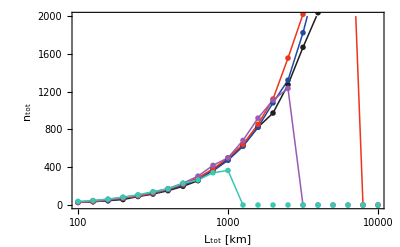

```mathematica
ListLogLinearPlot[Table[Transpose[{Ltot[[i]]/1*^3,ntot[[i]]}],{i,1,fileCounter}],PlotRange->{{Ltot[[1,1]]/1*^3,Ltot[[1,-1]]/1*^3},{1,2000}},GridLines->{All,All},PlotMarkers->plotmarkers,Joined->True,Frame->True,FrameLabel->{"L_tot [km]","n_tot"},ImageSize->imagesize,FrameTicks->{Automatic,{myTicks,None}},PlotStyle->plotstyle,LabelStyle->labelstyle,PlotLegends->plotlegends]
```

```mathematica
Export["C:\\Users\\SBihan\\Desktop\\Plots\\ntot\\ntot_7-1-3.svg",%219,"SVG"]
```

#### Plot c

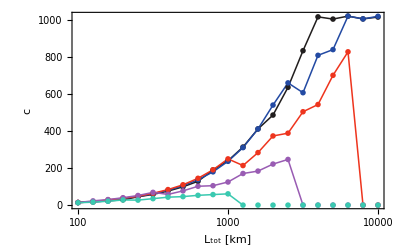

```mathematica
plot…c=ListLogLinearPlot[Table[Transpose[{Ltot[[i]]/1*^3,c[[i]]}],{i,1,fileCounter}], Background->background,PlotRange->{{Ltot[[1,1]]/1*^3,Ltot[[1,-1]]/1*^3},{1,Max[c]}},GridLines->{All,All},PlotMarkers->plotmarkers,Joined->True,Frame->True,FrameLabel->{"L_tot [km]","c"},ImageSize->imagesize,FrameTicks->{Automatic,{myTicks,None}},PlotStyle->plotstyle,LabelStyle->labelstyle,PlotLegends->plotlegends]
(*Export["C:\\Users\\jen_7\\Documents\\GitHub\\one-way-quantum-repeaters\\plot_c.pdf",plot…c];*)
```

```mathematica
Export["C:\\Users\\SBihan\\Desktop\\Plots\\c\\c_7-1-3.svg",plot…c,"SVG"]
```

#### Plot n

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

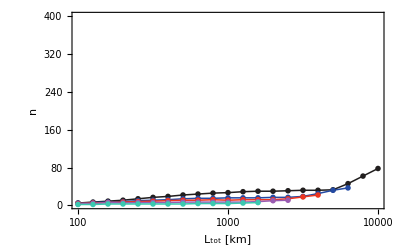

```mathematica
ListLogLinearPlot[Table[Transpose[{Ltot[[i]]/1*^3,Floor[ntot[[i]]/c[[i]]]}],{i,1,fileCounter}], Background->background,PlotRange->{{Ltot[[1,1]]/1*^3,Ltot[[1,-1]]/1*^3},{1,400}},GridLines->{All,All},PlotMarkers->plotmarkers,Joined->True,Frame->True,FrameLabel->{"L_tot [km]","n"},ImageSize->imagesize,FrameTicks->{Automatic,{myTicks,None}},PlotStyle->plotstyle,LabelStyle->labelstyle,PlotLegends->plotlegends]
```

#### Plot ∑p_trans

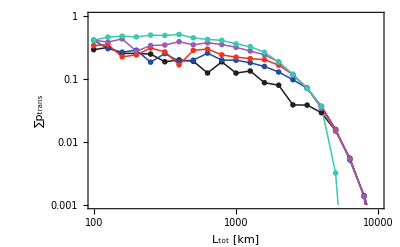

```mathematica
plottitle=Style["Message Transmission Probability Characteristics",Bold,Black,18,FontFamily->"Times"];

ListLogLogPlot[Table[Transpose[{Ltot[[i]]/1*^3,pTransSum[[i]]}],{i,1,fileCounter}], Background->background,PlotRange->{{Ltot[[1,1]]/1*^3,Ltot[[1,-1]]/1*^3},{1*^-3,1}},GridLines->{All,All},PlotMarkers->plotmarkers,Joined->True,Frame->True,FrameLabel->{Style["L_tot [km]",Bold,Black,axistitlefontsize,FontFamily->"Times"],Style["∑p_trans",Bold,Black,axistitlefontsize,FontFamily->"Times"]},ImageSize->imagesize,FrameTicksStyle->{{Directive[Black,FontSize->tickfontsize],Automatic},{Directive[Black,FontSize->tickfontsize],Automatic}},FrameTicks->{Automatic,{myTicks,None}},PlotStyle->plotstyle,LabelStyle->labelstyle,FrameStyle->framestyle,PlotLegends->Placed[plotlegends,{0.18,0.36}],PlotRangePadding->{{0.1,0.1},{0.25,0.1}}]
```

```mathematica
Export["E:\\Documents\\OneDrive - bracu.ac.bd\\Documents\\Quantum Computing\\Paper-Springer\\Corrected\\Plots (SVG)\\ptrans_7-1-3.svg",%768,"SVG"]
```

E:\Documents\OneDrive - bracu.ac.bd\Documents\Quantum Computing\Paper-Springer\Corrected\Plots (SVG)\ptrans_7-1-3.svg

#### Plot logical error

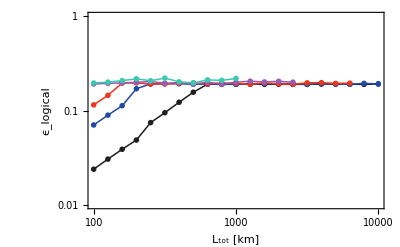

```mathematica
ListLogLogPlot[Table[Transpose[{Ltot[[i]]/1*^3,logicalError[[i]]}],{i,1,fileCounter}], Background->background,PlotRange->{{Ltot[[1,1]]/1*^3,Ltot[[1,-1]]/1*^3},{0.01,1}},GridLines->{All,All},PlotMarkers->plotmarkers,Joined->True,Frame->True,FrameLabel->{"L_tot [km]","\!\(\*SubscriptBox[\(ϵ\), \(logical\)]\)"},ImageSize->imagesize,FrameTicks->{Automatic,{myTicks,None}},PlotStyle->plotstyle,LabelStyle->labelstyle,PlotLegends->plotlegends]
```

```mathematica
Export["C:\\Users\\SBihan\\Desktop\\Plots\\Logical Error\\Logical-Error_7-1-3.svg",%210,"SVG"]
```

```mathematica
Export["C:\\Users\\SBihan\\Desktop\\Plots\\Logical Error\\Logical-Error_5-1-3.svg",%117,"SVG"]
```

#### Plot f

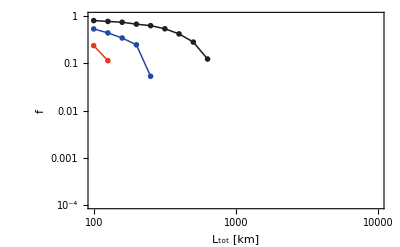

```mathematica
ListLogLogPlot[Table[Transpose[{Ltot[[i]]/1*^3,f[[i]]}],{i,1,fileCounter}],PlotRange->{{Ltot[[1,1]]/1*^3,Ltot[[1,-1]]/1*^3},{1*^-4,1}},GridLines->{All,All},PlotMarkers->plotmarkers,Joined->True,Frame->True,FrameLabel->{"L_tot [km]","f"},ImageSize->imagesize,FrameTicks->{Automatic,{myTicks,None}},PlotStyle->plotstyle,LabelStyle->labelstyle,PlotLegends->plotlegends]
```

```mathematica
Export["C:\\Users\\SBihan\\Desktop\\Plots\\SKF\\f_7-1-3.svg",%225,"SVG"]
```

C:\Users\SBihan\Desktop\Plots\SKF\f_7-1-3.svg

#### Plot η_e

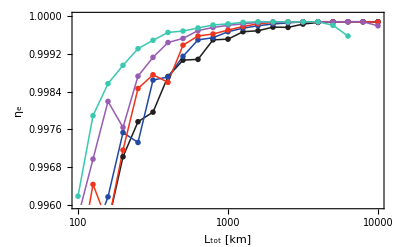

```mathematica
plottitle=Style["Tree Transmission Probability Characteristics",Bold,Black,18,FontFamily->"Times"];
ListLogLinearPlot[Table[Transpose[{Ltot[[i]]/1*^3,etae[[i]]}],{i,1,fileCounter}],PlotRange->{{Ltot[[1,1]]/1*^3,Ltot[[1,-1]]/1*^3},{0.996,1}}, Background->background,GridLines->{All,All},PlotMarkers->plotmarkers,Joined->True,Frame->True,FrameLabel->{Style["L_tot [km]",Bold,Black,axistitlefontsize,FontFamily->"Times"],Style["η_e",Bold,Black,axistitlefontsize,FontFamily->"Times"]},ImageSize->imagesize,FrameTicksStyle->{{Directive[Black,FontSize->tickfontsize],Automatic},{Directive[Black,FontSize->tickfontsize],Automatic}},FrameTicks->{Automatic,{myTicks,None}},PlotStyle->plotstyle,LabelStyle->labelstyle,FrameStyle->framestyle,PlotLegends->Placed[plotlegends,{0.83,0.4}]]
```

```mathematica
Export["E:\\Documents\\OneDrive - bracu.ac.bd\\Documents\\Quantum Computing\\Paper-Springer\\Corrected\\Plots (SVG)\\eta_e_7-1-3.svg",%770,"SVG"]
```

E:\Documents\OneDrive - bracu.ac.bd\Documents\Quantum Computing\Paper-Springer\Corrected\Plots (SVG)\eta_e_7-1-3.svg

```mathematica
If[doExport,
Quiet[mIItomI=c/(ntot-c),General::infy];
Quiet[mI=ntot-c,General::infy];
If[SameQ[binaryDataPathSuffix,"_maxSKR"]∨SameQ[StringTake[fileSuffix,-7],"_maxSKR"],
Print["Perform cost function calculation within Mathematica"];
cost=costFunc[SKR,Latt,1,tauph,Ltot,mI,c];];

Do[Export[NotebookDirectory[]<>"\\tex\\"<>binaryDataPath<>"_"<>fileHash<>"\\"<>filePrefix<>"SKR"<>fileSuffix<>"\\"<>filePrefix<>"SKR_reencodingError"<>ToString[reencodingError[[i]]]<>fileSuffix<>".csv",Prepend[Transpose[{Ltot[[i]]/1*^3,SKR[[i]]}],{"Ltot","SKR"}]],{i,1,Length[reencodingError]}];
Print["SKR data saved in .csv format!"];

Do[Export[NotebookDirectory[]<>"\\tex\\"<>binaryDataPath<>"_"<>fileHash<>"\\"<>filePrefix<>"cost"<>fileSuffix<>"\\"<>filePrefix<>"cost_reencodingError"<>ToString[reencodingError[[i]]]<>fileSuffix<>".csv",Prepend[Transpose[{Ltot[[i]]/1*^3,cost[[i]]}],{"Ltot","cost"}]],{i,1,Length[reencodingError]}];
Print["cost data saved in .csv format!"];

Do[Export[NotebookDirectory[]<>"\\tex\\"<>binaryDataPath<>"_"<>fileHash<>"\\"<>filePrefix<>"L0"<>fileSuffix<>"\\"<>filePrefix<>"L0_reencodingError"<>ToString[reencodingError[[i]]]<>fileSuffix<>".csv",Prepend[Transpose[{Ltot[[i]]/1*^3,L0[[i]]/1*^3}],{"Ltot","L0"}]],{i,1,Length[reencodingError]}];
Print["L0 data saved in .csv format!"];

Do[Export[NotebookDirectory[]<>"\\tex\\"<>binaryDataPath<>"_"<>fileHash<>"\\"<>filePrefix<>"mII"<>fileSuffix<>"\\"<>filePrefix<>"mII_reencodingError"<>ToString[reencodingError[[i]]]<>fileSuffix<>".csv",Prepend[Transpose[{Ltot[[i]]/1*^3,c[[i]]}],{"Ltot","mII"}]],{i,1,Length[reencodingError]}];
Print["Number of type II stations data saved in .csv format!"];

Do[Export[NotebookDirectory[]<>"\\tex\\"<>binaryDataPath<>"_"<>fileHash<>"\\"<>filePrefix<>"ntot"<>fileSuffix<>"\\"<>filePrefix<>"ntot_reencodingError"<>ToString[reencodingError[[i]]]<>fileSuffix<>".csv",Prepend[Transpose[{Ltot[[i]]/1*^3,ntot[[i]]}],{"Ltot","ntot"}]],{i,1,Length[reencodingError]}];
Print["Total number of stations data saved in .csv format!"];

Do[Export[NotebookDirectory[]<>"\\tex\\"<>binaryDataPath<>"_"<>fileHash<>"\\"<>filePrefix<>"mII-to-mI"<>fileSuffix<>"\\"<>filePrefix<>"mII-to-mI-ratio_reencodingError"<>ToString[reencodingError[[i]]]<>fileSuffix<>".csv",Prepend[Transpose[{Ltot[[i]]/1*^3,N[mIItomI[[i]]]}],{"Ltot","mII/mI"}]],{i,1,Length[reencodingError]}];
Print["mII/mI ratio data saved in .csv format!"];

Do[Export[NotebookDirectory[]<>"\\tex\\"<>binaryDataPath<>"_"<>fileHash<>"\\"<>filePrefix<>"mI"<>fileSuffix<>"\\"<>filePrefix<>"mI_reencodingError"<>ToString[reencodingError[[i]]]<>fileSuffix<>".csv",Prepend[Transpose[{Ltot[[i]]/1*^3,N[mI[[i]]]}],{"Ltot","mI"}]],{i,1,Length[reencodingError]}];
Print["mI data saved in .csv format!"];

RunProcess[{"pwsh","-File",".\\process-csv.ps1"},"StandardOutput"];
,Print["Export turned off!"];];
```

#### Unique tree vectors, sorted with ascending order w.r.t photon number.

```mathematica
uniqueTreeVecs=DeleteDuplicatesBy[#[[{1,2,3}]]&]@Flatten[treeVecs,1];
sortedUniqueTreeVecs=SortBy[uniqueTreeVecs,GetPhotonNumber[#]&];
treeVecsIndexing=(treeVecs/.Join[{sortedUniqueTreeVecs[[1]]->Indeterminate},Table[sortedUniqueTreeVecs[[i]]->(i-1),{i,2,Length[sortedUniqueTreeVecs]}]]);
If[doExport,Do[Export[NotebookDirectory[]<>"\\tex\\"<>binaryDataPath<>"_"<>fileHash<>"\\"<>filePrefix<>"treeVecs"<>fileSuffix<>"\\"<>filePrefix<>"treeVecs_reencodingError"<>ToString[reencodingError[[i]]]<>fileSuffix<>".csv",Prepend[Transpose[{Ltot[[i]]/1*^3,treeVecsIndexing[[i]]}],{"Ltot","treeIndexing"}]],{i,1,Length[reencodingError]}];
Print["Tree vector data saved in .csv format!"];
RunProcess[{"pwsh","-File",NotebookDirectory[]<>"\\process-csv.ps1"},"StandardOutput"];
];
sortedUniqueTreeVecs//MatrixForm
```

StringJoin::string: String expected at position 2 in D:\QEC_Codes\Thesis\Scripts\\tex\<>binaryDataPath<>_d525dbf2\<>filePrefix<>treeVecs<>fileSuffix<>\<>filePrefix<>treeVecs_reencodingError0.0001<>fileSuffix<>.csv.

StringJoin::string: String expected at position 4 in D:\QEC_Codes\Thesis\Scripts\\tex\<>binaryDataPath<>_d525dbf2\<>filePrefix<>treeVecs<>fileSuffix<>\<>filePrefix<>treeVecs_reencodingError0.0001<>fileSuffix<>.csv.

StringJoin::string: String expected at position 6 in D:\QEC_Codes\Thesis\Scripts\\tex\<>binaryDataPath<>_d525dbf2\<>filePrefix<>treeVecs<>fileSuffix<>\<>filePrefix<>treeVecs_reencodingError0.0001<>fileSuffix<>.csv.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Export::chtype: The first argument D:\QEC_Codes\Thesis\Scripts\\tex\<>binaryDataPath<>_d525dbf2\<>filePrefix<>treeVecs<>fileSuffix<>\<>filePrefix<>treeVecs_reencodingError0.0001<>fileSuffix<>.csv is not a valid file specification.

Export::chtype: The first argument D:\QEC_Codes\Thesis\Scripts\\tex\<>binaryDataPath<>_d525dbf2\<>filePrefix<>treeVecs<>fileSuffix<>\<>filePrefix<>treeVecs_reencodingError0.0003<>fileSuffix<>.csv is not a valid file specification.

Export::chtype: The first argument D:\QEC_Codes\Thesis\Scripts\\tex\<>binaryDataPath<>_d525dbf2\<>filePrefix<>treeVecs<>fileSuffix<>\<>filePrefix<>treeVecs_reencodingError0.0005<>fileSuffix<>.csv is not a valid file specification.

General::stop: Further output of Export::chtype will be suppressed during this calculation.

Tree vector data saved in .csv format!

(0 | 0 | 0
4 | 9 | 4
4 | 10 | 4
3 | 14 | 4
4 | 11 | 4
4 | 12 | 4
4 | 13 | 4
5 | 11 | 4
4 | 14 | 4)

#### Get the string to put in pgfplot settings.

```mathematica
Clear[treeString];
treeString="";
Do[
treeString=treeString<>"{$[";
Do[
treeString=If[SameQ[j,Dimensions[sortedUniqueTreeVecs][[2]]],treeString<>ToString[sortedUniqueTreeVecs[[i,j]]],treeString<>ToString[sortedUniqueTreeVecs[[i,j]]]<>",\!"];
,{j,1,Dimensions[sortedUniqueTreeVecs][[2]]}];
treeString=treeString<>"]$}";
If[¬SameQ[i,Dimensions[sortedUniqueTreeVecs][[1]]],treeString=treeString<>","];
,{i,2,Dimensions[sortedUniqueTreeVecs][[1]]}];

Print["ymin=",0.5,",\n","ymax=",Length[sortedUniqueTreeVecs]-0.5,",\n","ytick="<>StringReplace[ToString[Table[i,{i,1,Length[sortedUniqueTreeVecs]-1}]]," "->""]<>",\n","yticklabels={"<>treeString<>"},"]
```

```mathematica
sortedUniqueTreeVecs
```